## Parton Level Cross Section

The parton - level cross section can be evaluated by using two Fourier Transforms :

### -Graphics-

```mathematica
F1[x_,y_]=FourierTransform[1/(lx^2+ly^2),{lx,ly},{x,y}]
```

1/2 (-HeavisideTheta[-x] (2 EulerGamma+2 Log[-x]+Log[1+y^2/x^2])-HeavisideTheta[x] (2 EulerGamma+2 Log[x]+Log[1+y^2/x^2]))

It only depends on r=√(x^2+y^2) as it should.

```mathematica
F1[r_]=1/(2π)(-EulerGamma-Log[r])
```

(-EulerGamma-Log[r])/(2 π)

```mathematica
Ω[d_]:=(2 π^(d/2))/Gamma[d/2]
```

```mathematica
setd:={d->2+2ϵ}
```

```mathematica
F1DR=1/2 μ^(2-d)Ω[d-1]/(2π)^(d-1) r^(-(d-2))Gamma[d-2]/.setd//FullSimplify
```

1/4 π^(-1-ϵ) r^(-2 ϵ) μ^(-2 ϵ) Gamma[ϵ]

## -Graphics-

We would like to evalue the Fourier Transform of (k<->l compared to the note)

```mathematica
itg:=1/(lx^2+ly^2)1/((lx-kx)^2+(ly-ky)^2)
```

Let us choose a frame in which (x,y)=(0, r). In this frame, (kx, ky) = (|k⃗-k⃗.x⃗x⃗/r^2|, k⃗.x⃗/r)
Then it is trivial to integrate out lx first. We close the integration contour upward in the complex plane:

```mathematica
intkxana[ly_,{kx_,ky_}]=I Factor[HeavisideTheta[ly]Residue[itg,{lx,I ly}]]+I Factor[HeavisideTheta[-ly]Residue[itg,{lx,-I ly}]]+I Factor[HeavisideTheta[ly-ky]Residue[itg,{lx,kx+I (ly-ky)}]]+I Factor[HeavisideTheta[-ly+ky]Residue[itg,{lx,kx-I (ly-ky)}]]
```

(ⅈ HeavisideTheta[ky-ly])/(2 (kx+ⅈ ky) (ky-ly) (ⅈ kx-ky+2 ly))+(ⅈ HeavisideTheta[-ly])/(2 (kx+ⅈ ky) ly (-ⅈ kx-ky+2 ly))+(ⅈ HeavisideTheta[ly])/(2 (kx-ⅈ ky) ly (ⅈ kx-ky+2 ly))+(ⅈ HeavisideTheta[-ky+ly])/(2 (kx-ⅈ ky) (ky-ly) (-ⅈ kx-ky+2 ly))

That is,

```mathematica
ftkx:=(ⅈ HeavisideTheta[ky-ly])/(2 (kx+ⅈ ky) (ky-ly) (ⅈ kx-ky+2 ly))+(ⅈ HeavisideTheta[-ly])/(2 (kx+ⅈ ky) ly (-ⅈ kx-ky+2 ly))+(ⅈ HeavisideTheta[ly])/(2 (kx-ⅈ ky) ly (ⅈ kx-ky+2 ly))+(ⅈ HeavisideTheta[-ky+ly])/(2 (kx-ⅈ ky) (ky-ly) (-ⅈ kx-ky+2 ly))
```

```mathematica
intkx[ly_,{kx_,ky_}]:=1/(2π)NIntegrate[1/(lx^2+ly^2)1/((lx-kx)^2+(ly-ky)^2),{lx,-Infinity,Infinity}]
```

Check :

```mathematica
intkxana[0.1,{0.2,0.3}]
intkx[0.1,{0.2,0.3}]
```

57.6923+3.55271×10^-15 ⅈ

57.6923

```mathematica
cond:=r>0&&x∈Reals&&y∈Reals&&2 π>ϕ>0 &&ly∈Reals&&kx∈Reals&&ky∈Reals
```

the first term

let us introduce a regulator

```mathematica
reg[ly_]:=(ly^2 (ly-ky)^2)^ϵ
```

#### Term 1: residue of lx = -i ly

```mathematica
ftkx[[2]]
```

(ⅈ HeavisideTheta[-ly])/(2 (kx+ⅈ ky) ly (-ⅈ kx-ky+2 ly))

Let us decompose it into two terms :

```mathematica
Apart[ftkx[[2]],ly]
```

-HeavisideTheta[-ly]/(2 (kx-ⅈ ky) (kx+ⅈ ky) ly)+HeavisideTheta[-ly]/((kx-ⅈ ky) (kx+ⅈ ky) (-ⅈ kx-ky+2 ly))

Let us take out the k-dependent terms:

```mathematica
dem:=2 ly (2 ly-ⅈ kx-ky) (kx+ⅈ ky)
```

```mathematica
apky= Apart[((kx-ⅈ ky) (kx+ⅈ ky))/dem,ly]
```

ⅈ/(2 ly)-ⅈ/(-ⅈ kx-ky+2 ly)

```mathematica
term11=ftkx[[2]] dem apky[[1]]
```

-HeavisideTheta[-ly]/(2 ly)

The first term with 1/(√(2π)) due to the normalization of FourierTransform:

```mathematica
Term11=Assuming[cond,1/(k^2 (2π)^(1/2))FourierTransform[term11,ly,r]//FullSimplify]
```

-(EulerGamma+(ⅈ π)/2+Log[r])/(4 k^2 π)

The second term :

```mathematica
term12=ftkx[[2]] dem apky[[2]]
```

HeavisideTheta[-ly]/(-ⅈ kx-ky+2 ly)

```mathematica
Term12F=Assuming[cond,1/(k^2 (2π)^(1/2))FourierTransform[term12,ly,r]//FullSimplify]
```

(ⅇ^(-1/2 (kx-ⅈ ky) r) (ⅈ π+2 CosIntegral[1/2 (ⅈ kx+ky) r]+2 SinhIntegral[1/2 (kx-ⅈ ky) r]))/(8 k^2 π)

Let us try another way (convolution theorem):
∫dl/(2π)ⅇ^ⅈlr f_1(l)f_2(l)=∫dr_1(f̃)_1(r_1)(f̃)_2(r-r_1)

```mathematica
Numerator[ftkx[[2]] dem apky[[2]]]
```

HeavisideTheta[-ly]

```mathematica
f2[y_]=FullSimplify[Expand[1/(√(2 π))FourierTransform[HeavisideTheta[-ly],ly,y]]]
f1[y_]=Assuming[cond,FullSimplify[Expand[1/(√(2 π))FourierTransform[term12/HeavisideTheta[-ly],ly,y]]]]
```

-ⅈ/(2 π y)+DiracDelta[y]/2

1/2 ⅈ ⅇ^(-1/2 (kx-ⅈ ky) y) HeavisideTheta[y Sign[kx]] Sign[kx]

```mathematica
Integrate[(f1[y]/.{Sign[kx]-> 1})f2[r-y] ,{y,-Infinity,Infinity}]
Integrate[(f1[y]/.{Sign[kx]-> -1})f2[r-y] ,{y,-Infinity,Infinity}]
```

ConditionalExpression[-(ⅇ^(-1/2 (kx-ⅈ ky) r) Gamma[0,-1/2 (kx-ⅈ ky) r])/(4 π),Im[ky]+Re[kx]>0&&Re[r]<0&&Im[r]==0]

ConditionalExpression[-(ⅇ^(-1/2 (kx-ⅈ ky) r) Gamma[0,-1/2 (kx-ⅈ ky) r])/(4 π),Im[ky]+Re[kx]<0&&Re[r]>0&&Im[r]==0]

```mathematica
Term12:=-(ⅇ^(-1/2 (kx-ⅈ ky) r) Gamma[0,-1/2 (kx-ⅈ ky) r])/(4 π k^2)
```

```mathematica
Term12/.{k->1.0, kx->0.1, ky->0.2, r->3}
Term12F/.{k->1.0, kx->0.1, ky->0.2, r->3}
```

-0.0597985+0.104276 ⅈ

-0.0597985+0.104276 ⅈ

```mathematica
term1=Term11+Term12
```

-(ⅇ^(-1/2 (kx-ⅈ ky) r) Gamma[0,-1/2 (kx-ⅈ ky) r])/(4 k^2 π)-(EulerGamma+(ⅈ π)/2+Log[r])/(4 k^2 π)

Check :

```mathematica
1/(kx^2+ky^2)(term11+term12)-ftkx[[2]]//FullSimplify
```

0

#### Term 2

```mathematica
ftkx[[3]]
```

(ⅈ HeavisideTheta[ly])/(2 (kx-ⅈ ky) ly (ⅈ kx-ky+2 ly))

```mathematica
Denominator[ftkx[[3]]]
```

2 (kx-ⅈ ky) ly (ⅈ kx-ky+2 ly)

```mathematica
apky= Apart[((kx-ⅈ ky) (kx+ⅈ ky))/Denominator[ftkx[[3]]],ly]
```

-ⅈ/(2 ly)+ⅈ/(ⅈ kx-ky+2 ly)

```mathematica
term21=Numerator[ftkx[[3]]] apky[[1]]
term22=Numerator[ftkx[[3]]] apky[[2]]
```

HeavisideTheta[ly]/(2 ly)

-HeavisideTheta[ly]/(ⅈ kx-ky+2 ly)

Check :

```mathematica
1/(kx^2+ky^2)(term21+term22)-ftkx[[3]]//FullSimplify
```

0

```mathematica
Term21=Assuming[cond,1/(k^2 √(2 π))FourierTransform[term21,ly,r]//FullSimplify]
```

-(2 EulerGamma-ⅈ π+2 Log[r])/(8 k^2 π)

It can also be obtained by symmetry :

```mathematica
(term11/.{ly-> -ly})-term21
```

0

Therefore, we should have
Term21 = -Term11/.{r->-r}

```mathematica
Term21 -Assuming[k>0&&r>0,Conjugate[Term11]//FullSimplify]//FullSimplify
```

0

```mathematica
Term22F=Assuming[cond,1/(k^2 √(2 π))FourierTransform[term22,ly,r]//FullSimplify]
```

(ⅇ^(1/2 (kx+ⅈ ky) r) (-ⅈ π+2 CosIntegral[1/2 ⅈ (kx+ⅈ ky) r]-2 SinhIntegral[1/2 (kx+ⅈ ky) r]))/(8 k^2 π)

```mathematica
term12
term22
```

HeavisideTheta[-ly]/(-ⅈ kx-ky+2 ly)

-HeavisideTheta[ly]/(ⅈ kx-ky+2 ly)

```mathematica
(term12/.{ly-> -ly,kx->kx,ky->-ky})-term22//FullSimplify
```

0

```mathematica
d22=Term22F -Assuming[k>0&&r>0&&kx∈Reals&&ky∈Reals,Term12/.{kx->kx,ky->-ky,r->-r}//FullSimplify]//FullSimplify
```

(ⅇ^(1/2 (kx+ⅈ ky) r) (-ⅈ π+2 Log[ⅈ (kx+ⅈ ky) r]-2 Log[(kx+ⅈ ky) r]))/(8 k^2 π)

```mathematica
d22/.{r->3.0, kx->0.5, ky->-2.0}
```

(5.27886×10^-18-3.70325×10^-17 ⅈ)/k^2

```mathematica
term21
```

HeavisideTheta[ly]/(2 ly)

```mathematica
term22
```

-HeavisideTheta[ly]/(ⅈ kx-ky+2 ly)

```mathematica
f22[y_]=FullSimplify[Expand[1/(√(2 π))FourierTransform[HeavisideTheta[ly],ly,y]]]
f21[y_]=Assuming[cond,FullSimplify[Expand[1/(√(2 π))FourierTransform[term22/HeavisideTheta[ly],ly,y]]]]
```

ⅈ/(2 π y)+DiracDelta[y]/2

1/2 ⅈ ⅇ^(1/2 (kx+ⅈ ky) y) HeavisideTheta[-y Sign[kx]] Sign[kx]

```mathematica
Integrate[(f21[y]/.{Sign[kx]-> 1})f22[r-y] ,{y,-Infinity,Infinity}]
Integrate[(f21[y]/.{Sign[kx]-> -1})f22[r-y] ,{y,-Infinity,Infinity}]
```

ConditionalExpression[-(ⅇ^(1/2 (kx+ⅈ ky) r) Gamma[0,1/2 (kx+ⅈ ky) r])/(4 π),Re[kx]>Im[ky]&&Re[r]>0&&Im[r]==0]

ConditionalExpression[-(ⅇ^(1/2 (kx+ⅈ ky) r) Gamma[0,1/2 (kx+ⅈ ky) r])/(4 π),Re[kx]<Im[ky]&&Re[r]<0&&Im[r]==0]

```mathematica
Term12
```

-(ⅇ^(-1/2 (kx-ⅈ ky) r) Gamma[0,-1/2 (kx-ⅈ ky) r])/(4 k^2 π)

```mathematica
Term22:=-(ⅇ^(1/2 (kx+ⅈ ky) r) Gamma[0,1/2 (kx+ⅈ ky) r])/(4 π k^2)
```

```mathematica
Term22F/.{kx->3,ky->0.3,r->1.0}
Term22/.{kx->3,ky->0.3,r->1.0}
```

-(0.0354701-0.00259079 ⅈ)/k^2

-(0.0354701-0.00259079 ⅈ)/k^2

```mathematica
term2=Term21+Term22
```

-(ⅇ^(1/2 (kx+ⅈ ky) r) Gamma[0,1/2 (kx+ⅈ ky) r])/(4 k^2 π)-(2 EulerGamma-ⅈ π+2 Log[r])/(8 k^2 π)

```mathematica
ftkx[[2;;3]]
```

(ⅈ HeavisideTheta[-ly])/(2 (kx+ⅈ ky) ly (-ⅈ kx-ky+2 ly))+(ⅈ HeavisideTheta[ly])/(2 (kx-ⅈ ky) ly (ⅈ kx-ky+2 ly))

From this, we can see how the two related to each other :

```mathematica
(Assuming[cond,Conjugate[ftkx[[1]]]//FullSimplify]/.Conjugate[x_]->x/.{ky->-ky}//FullSimplify)/.{lx->-lx,ly->-ly}//FullSimplify
```

-HeavisideTheta[-ky+ly]/(2 (kx+ⅈ ky) (kx+ⅈ (ky-2 ly)) (ky-ly))

```mathematica
ftkx[[3]]
```

(ⅈ HeavisideTheta[ly])/(2 (kx-ⅈ ky) ly (ⅈ kx-ky+2 ly))

```mathematica
(ⅈ HeavisideTheta[ly])/(2 ly (2 ly+ⅈ kx-ky) (kx-ⅈ ky))-ftkx[[3]]
```

0

```mathematica
((Assuming[cond&&l>0,Conjugate[term1]//FullSimplify])/.{lx->-lx,ly->-ly}//FullSimplify)/.Conjugate[Gamma[0,1/2 (lx-ⅈ ly) r]]->Gamma[0,1/2 (lx+ⅈ ly) r]
```

-(2 EulerGamma-ⅈ π+2 ⅇ^(1/2 (lx+ⅈ ly) r) Gamma[0,1/2 (lx+ⅈ ly) r]+2 Log[r])/(4 l^2 √(2 π))

```mathematica
-(2 EulerGamma-ⅈ π+2 ⅇ^(1/2 (lx+ⅈ ly) r) Gamma[0,1/2 (lx+ⅈ ly) r]+2 Log[r])/(4 l^2 √(2 π))-term2//FullSimplify
```

0

Check!

#### Term 3

```mathematica
ftkx
```

(ⅈ HeavisideTheta[-ky])/(2 ky (2 ky-ⅈ lx-ly) (lx+ⅈ ly))+(ⅈ HeavisideTheta[ky])/(2 ky (2 ky+ⅈ lx-ly) (lx-ⅈ ly))+HeavisideTheta[ky-ly]/(2 (ky-ly) (2 ky-ⅈ lx-ly) (ⅈ lx+ly))-HeavisideTheta[-ky+ly]/(2 (ky-ly) (lx+ⅈ ly) (-2 ⅈ ky+lx+ⅈ ly))

```mathematica
((FullSimplify[(ftkx[[3]]/.{ky->ky+ly})]))-(ftkx[[2]]/.{lx->-lx,ly->-ly})//FullSimplify
```

0

This tells us that

```mathematica
term3=FullSimplify[Exp[I ly r] (term2/.{lx->-lx,ly->-ly})]
```

-(ⅇ^(ⅈ ly r) (2 EulerGamma-ⅈ π+2 ⅇ^(-1/2 (lx+ⅈ ly) r) Gamma[0,-1/2 (lx+ⅈ ly) r]+2 Log[r]))/(4 l^2 √(2 π))

#### Term 4

```mathematica
((FullSimplify[(ftkx[[4]]/.{ky->ky+ly})]))-(ftkx[[1]]/.{lx->-lx,ly->-ly})//FullSimplify
```

0

```mathematica
term4=FullSimplify[Exp[I ly r] (term1/.{lx->-lx,ly->-ly})]
```

-(ⅇ^(ⅈ ly r) (2 EulerGamma+ⅈ π+2 ⅇ^(1/2 (lx-ⅈ ly) r) Gamma[0,1/2 (lx-ⅈ ly) r]+2 Log[r]))/(4 l^2 √(2 π))

```mathematica
cond
```

r>0&&x∈Reals&&y∈Reals&&2 π>ϕ>0&&ky∈Reals&&lx∈Reals&&ly∈Reals

### Final

```mathematica
final=Expand[Assuming[cond,Simplify[Sqrt[2π] (term1+term2+term3+term4)]]]
```

-EulerGamma/l^2-(ⅇ^(ⅈ ly r) EulerGamma)/l^2-(ⅇ^(-1/2 (lx-ⅈ ly) r) Gamma[0,-1/2 (lx-ⅈ ly) r])/(2 l^2)-(ⅇ^(1/2 (lx+ⅈ ly) r) Gamma[0,1/2 (lx-ⅈ ly) r])/(2 l^2)-(ⅇ^(-1/2 (lx-ⅈ ly) r) Gamma[0,-1/2 (lx+ⅈ ly) r])/(2 l^2)-(ⅇ^(1/2 (lx+ⅈ ly) r) Gamma[0,1/2 (lx+ⅈ ly) r])/(2 l^2)-Log[r]/l^2-(ⅇ^(ⅈ ly r) Log[r])/l^2

Note that this is the result for ϕx = π/2. lx=l cos(ϕl-π/2) and ly=l sin(ϕl-π/2).

```mathematica
ft02[{l_,ϕl_},{r_,ϕx_}]=((-EulerGamma/l^2-(ⅇ^(ⅈ ly r) EulerGamma)/l^2-(ⅇ^(-1/2 (lx-ⅈ ly) r) Gamma[0,-1/2 (lx-ⅈ ly) r])/(2 l^2)-(ⅇ^(1/2 (lx+ⅈ ly) r) Gamma[0,1/2 (lx-ⅈ ly) r])/(2 l^2)-(ⅇ^(-1/2 (lx-ⅈ ly) r) Gamma[0,-1/2 (lx+ⅈ ly) r])/(2 l^2)-(ⅇ^(1/2 (lx+ⅈ ly) r) Gamma[0,1/2 (lx+ⅈ ly) r])/(2 l^2)-Log[r]/l^2-(ⅇ^(ⅈ ly r) Log[r])/l^2)/.{lx->l Cos[ϕl-ϕx+π/2],ly->l Sin[ϕl-ϕx+π/2]})
```

-EulerGamma/l^2-(ⅇ^(ⅈ l r Cos[ϕl-ϕx]) EulerGamma)/l^2-(ⅇ^(-1/2 r (-ⅈ l Cos[ϕl-ϕx]-l Sin[ϕl-ϕx])) Gamma[0,-1/2 r (-ⅈ l Cos[ϕl-ϕx]-l Sin[ϕl-ϕx])])/(2 l^2)-(ⅇ^(1/2 r (ⅈ l Cos[ϕl-ϕx]-l Sin[ϕl-ϕx])) Gamma[0,1/2 r (-ⅈ l Cos[ϕl-ϕx]-l Sin[ϕl-ϕx])])/(2 l^2)-(ⅇ^(-1/2 r (-ⅈ l Cos[ϕl-ϕx]-l Sin[ϕl-ϕx])) Gamma[0,-1/2 r (ⅈ l Cos[ϕl-ϕx]-l Sin[ϕl-ϕx])])/(2 l^2)-(ⅇ^(1/2 r (ⅈ l Cos[ϕl-ϕx]-l Sin[ϕl-ϕx])) Gamma[0,1/2 r (ⅈ l Cos[ϕl-ϕx]-l Sin[ϕl-ϕx])])/(2 l^2)-Log[r]/l^2-(ⅇ^(ⅈ l r Cos[ϕl-ϕx]) Log[r])/l^2

```mathematica
ft01[{l_,ϕl_},{r_,ϕx_}]=(-EulerGamma-Log[r])/l^2
```

(-EulerGamma-Log[r])/l^2

```mathematica
F01[{x_,y_},{kx_,ky_}]:=Module[{r,ϕx,l,ϕk},
r=Sqrt[x^2+y^2];ϕx=ArcTan[x,y];
l=Sqrt[kx^2+ky^2];ϕk=ArcTan[kx,ky];
ft01[{l,ϕk},{r,ϕx}]
]
F02[{x_,y_},{kx_,ky_}]:=Module[{r,ϕx,l,ϕk},
r=Sqrt[x^2+y^2];ϕx=ArcTan[x,y];
l=Sqrt[kx^2+ky^2];ϕk=ArcTan[kx,ky];
ft02[{l,ϕk},{r,ϕx}]
]
```

```mathematica
ana[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{lx_,ly_}]:=( F01[{bx+x1-x3,by+y1-y3},{lx,ly}] Exp[-I (lx x1+ly y1)]-F01[{bx-x3+x2,by-y3+y2},{lx,ly}] Exp[-I (lx x2+ly y2)]-F01[{bx-x4+x1,by-y4+y1},{lx,ly}] Exp[-I (lx x1+ly y1)]+F01[{bx-x4+x2,by-y4+y2},{lx,ly}] Exp[-I (lx x2+ly y2)])-( F02[{bx+x1-x3,by+y1-y3},{lx,ly}] Exp[-I (lx x1+ly y1)]-F02[{bx-x3+x2,by-y3+y2},{lx,ly}] Exp[-I (lx x2+ly y2)]-F02[{bx-x4+x1,by-y4+y1},{lx,ly}] Exp[-I (lx x1+ly y1)]+F02[{bx-x4+x2,by-y4+y2},{lx,ly}] Exp[-I (lx x2+ly y2)])
```

```mathematica
num[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{lx_,ly_}]:=1/(2π)NIntegrate[Exp[I (bx kx+by ky)] 1/(kx^2+ky^2)(1/(lx^2+ly^2)-1/((kx-lx)^2+(ky-ly)^2)) (Exp[-I (kx x3+ ky y3)]-Exp[-I (kx x4+ ky y4)])(Exp[I ((kx-lx) x1+ (ky-ly) y1)]-Exp[I ((kx-lx) x2+ (ky-ly) y2)]),{kx,-Infinity,Infinity},{ky,-Infinity,Infinity}]
```

```mathematica
bu={3.0,0.1};
x1u={1.0,0.5};
x2u={1.5,0.25};
x3u={0.1,0.75};
x4u={1.3,2.5};
ku={2.2,1.8};
num[bu,x1u,x2u,x3u,x4u,{2.2,1.8}]
```

0.00511557+0.00174474 ⅈ

```mathematica
ana[bu,x1u,x2u,x3u,x4u,ku]
```

0.00511521+0.00174514 ⅈ

```mathematica
bu={1.0,-0.1};
x1u={1.3,0.45};
x2u={0.5,0.125};
x3u={0.31,0.5};
x4u={3.3,.5};
ku={2.3,0.8};
num[bu,x1u,x2u,x3u,x4u,ku]
ana[bu,x1u,x2u,x3u,x4u,ku]
```

0.289065+0.303098 ⅈ

0.289015+0.303045 ⅈ

## Dipole Radiation

```mathematica
F01R[{x_,y_},{kx_,ky_}]=Simplify[{kx,ky} F01[{x,y},{kx,ky}]]
```

{-(kx (2 EulerGamma+Log[x^2+y^2]))/(2 (kx^2+ky^2)),-(ky (2 EulerGamma+Log[x^2+y^2]))/(2 (kx^2+ky^2))}

```mathematica
F02R[{x_,y_},{kx_,ky_}]=Simplify[{kx,ky}F02[{x,y},{kx,ky}]+I{D[F02[{x,y},{kx,ky}],x],D[F02[{x,y},{kx,ky}],y]}]
```

{1/(4 (kx^2+ky^2))ⅇ^(1/2 (-ky x-kx y)) (-4 ⅇ^(1/2 (ky x+kx y)) EulerGamma kx-ⅇ^((ⅈ kx x)/2+ky x+(ⅈ ky y)/2) (kx+ⅈ ky) Gamma[0,1/2 (-ⅈ kx+ky) (x-ⅈ y)]-ⅇ^((ⅈ kx x)/2+ky x+(ⅈ ky y)/2) (kx+ⅈ ky) Gamma[0,1/2 (ⅈ kx+ky) (x+ⅈ y)]-ⅇ^((ⅈ kx x)/2+kx y+(ⅈ ky y)/2) kx Gamma[0,1/2 (kx-ⅈ ky) (-ⅈ x+y)]+ⅈ ⅇ^((ⅈ kx x)/2+kx y+(ⅈ ky y)/2) ky Gamma[0,1/2 (kx-ⅈ ky) (-ⅈ x+y)]-ⅇ^((ⅈ kx x)/2+kx y+(ⅈ ky y)/2) kx Gamma[0,1/2 (kx+ⅈ ky) (ⅈ x+y)]+ⅈ ⅇ^((ⅈ kx x)/2+kx y+(ⅈ ky y)/2) ky Gamma[0,1/2 (kx+ⅈ ky) (ⅈ x+y)]-2 ⅇ^(1/2 (ky x+kx y)) kx Log[x^2+y^2]),1/(4 (kx^2+ky^2))ⅇ^(1/2 (-ky x-kx y)) (-4 ⅇ^(1/2 (ky x+kx y)) EulerGamma ky+ⅈ ⅇ^((ⅈ kx x)/2+ky x+(ⅈ ky y)/2) (kx+ⅈ ky) Gamma[0,1/2 (-ⅈ kx+ky) (x-ⅈ y)]+ⅈ ⅇ^((ⅈ kx x)/2+ky x+(ⅈ ky y)/2) (kx+ⅈ ky) Gamma[0,1/2 (ⅈ kx+ky) (x+ⅈ y)]-ⅈ ⅇ^((ⅈ kx x)/2+kx y+(ⅈ ky y)/2) kx Gamma[0,1/2 (kx-ⅈ ky) (-ⅈ x+y)]-ⅇ^((ⅈ kx x)/2+kx y+(ⅈ ky y)/2) ky Gamma[0,1/2 (kx-ⅈ ky) (-ⅈ x+y)]-ⅈ ⅇ^((ⅈ kx x)/2+kx y+(ⅈ ky y)/2) kx Gamma[0,1/2 (kx+ⅈ ky) (ⅈ x+y)]-ⅇ^((ⅈ kx x)/2+kx y+(ⅈ ky y)/2) ky Gamma[0,1/2 (kx+ⅈ ky) (ⅈ x+y)]-2 ⅇ^(1/2 (ky x+kx y)) ky Log[x^2+y^2])}

```mathematica
numx[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{lx_,ly_}]:=NIntegrate[Exp[I (bx kx+by ky)] 1/(kx^2+ky^2)(lx/(lx^2+ly^2)-(lx-kx)/((kx-lx)^2+(ky-ly)^2)) (Exp[-I (kx x3+ ky y3)]-Exp[-I (kx x4+ ky y4)])(Exp[I ((kx-lx) x1+ (ky-ly) y1)]-Exp[I ((kx-lx) x2+ (ky-ly) y2)]),{kx,-Infinity,Infinity},{ky,-Infinity,Infinity}]
numy[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{lx_,ly_}]:=NIntegrate[Exp[I (bx kx+by ky)] 1/(kx^2+ky^2)(ly/(lx^2+ly^2)-(ly-ky)/((kx-lx)^2+(ky-ly)^2)) (Exp[-I (kx x3+ ky y3)]-Exp[-I (kx x4+ ky y4)])(Exp[I ((kx-lx) x1+ (ky-ly) y1)]-Exp[I ((kx-lx) x2+ (ky-ly) y2)]),{kx,-Infinity,Infinity},{ky,-Infinity,Infinity}]
ana[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kx_,ky_}]:=2π(( F01R[{bx+x1-x3,by+y1-y3},{kx,ky}] Exp[-I (kx x1+ky y1)]-F01R[{bx-x3+x2,by-y3+y2},{kx,ky}] Exp[-I (kx x2+ky y2)]-F01R[{bx-x4+x1,by-y4+y1},{kx,ky}] Exp[-I (kx x1+ky y1)]+F01R[{bx-x4+x2,by-y4+y2},{kx,ky}] Exp[-I (kx x2+ky y2)])-( F02R[{bx+x1-x3,by+y1-y3},{kx,ky}] Exp[-I (kx x1+ky y1)]-F02R[{bx-x3+x2,by-y3+y2},{kx,ky}] Exp[-I (kx x2+ky y2)]-F02R[{bx-x4+x1,by-y4+y1},{kx,ky}] Exp[-I (kx x1+ky y1)]+F02R[{bx-x4+x2,by-y4+y2},{kx,ky}] Exp[-I (kx x2+ky y2)]))
```

```mathematica
bu={1.0,-0.1};
x1u={1.3,0.45};
x2u={0.5,0.125};
x3u={0.31,0.5};
x4u={3.3,.5};
ku={2.3,0.8};
{numx[bu,x1u,x2u,x3u,x4u,ku],numy[bu,x1u,x2u,x3u,x4u,ku]}
ana[bu,x1u,x2u,x3u,x4u,ku]
```

{1.10543+1.10826 ⅈ,0.685803+1.1379 ⅈ}

{1.10543+1.10826 ⅈ,0.685803+1.1379 ⅈ}

```mathematica
dσ[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kT_,ϕ_}]:=Module[{amp},
amp=ana[{bx,by},{x1,y1},{x2,y2},{x3,y3},{x4,y4},{kT Cos[ϕ],kT Sin[ϕ]}];
amp.Conjugate[amp]
]
```

```mathematica
showdσ[bu_,x1u_,x2u_,x3u_,x4u_,kT_]:=Module[{ϕ},
Print[Show[Graphics[{Orange,Opacity[0.3],Disk[{0,0},0.6]}],Graphics[{Orange,Opacity[0.3],Disk[bu,0.6]}],Graphics[{Dashing[0.025],RGBColor[0,0.5,0],Thickness[0.01],Line[{x3u,x4u}]}],Graphics[{PointSize[0.05],Blue,Point[x3u]}],Graphics[{PointSize[0.05],Red,Point[x4u]}],Graphics[{Dashing[0.025],RGBColor[0,0.5,0],Thickness[0.01],Line[{bu+x3u,bu+x4u}]}],Graphics[{PointSize[0.05],Blue,Point[bu+x1u]}],Graphics[{PointSize[0.05],Red,Point[bu+x4u]}],Axes->True,LabelStyle->{Black,16},PlotLabel->"Dipole Orientation"]];
Print[""];
Print[ParametricPlot[dσ[bu,x1u,x2u,x3u,x4u,{kT,ϕ}]{Cos[ϕ],Sin[ϕ]},{ϕ,0,2π},PlotStyle->Red,AxesLabel->{x,y},LabelStyle->{Black,16},PlotLabel->"dσ/d^2{Cos[ϕ],Sin[ϕ]}"]];
Print["v_2=",NIntegrate[dσ[bu,x1u,x2u,x3u,x4u,{kT,ϕ}] Cos[2(ϕ)],{ϕ,0,2π}]/NIntegrate[dσ[bu,x1u,x2u,x3u,x4u,{kT,ϕ}],{ϕ,0,2π}]];
]
```

### kT~1/r

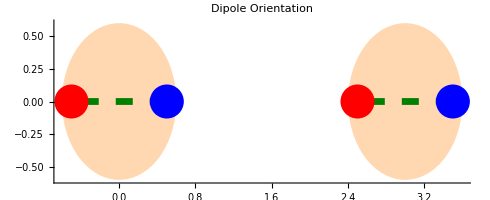

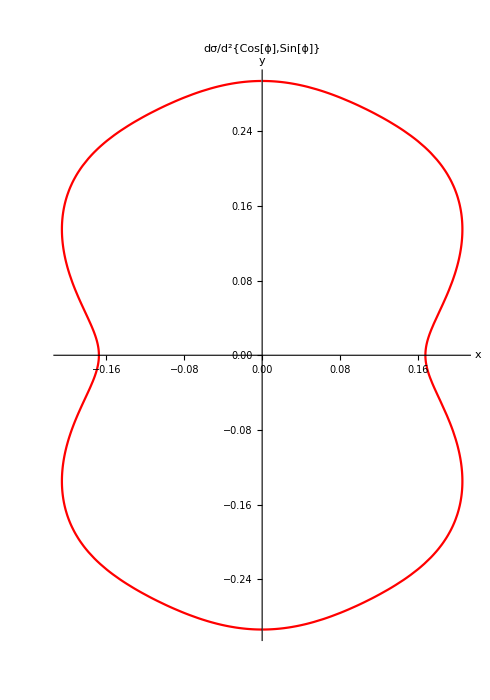

v_2=-0.114285-4.15293×10^-20 ⅈ

```mathematica
x1u={1/2,0};
x2u={-1/2,0};
x3u={1/2,0};
x4u={-1/2,0};
bu={3,0};
kT=1.0;
showdσ[bu,x1u,x2u,x3u,x4u,kT]
```

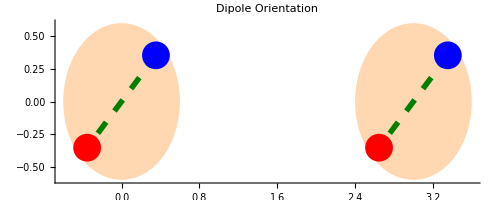

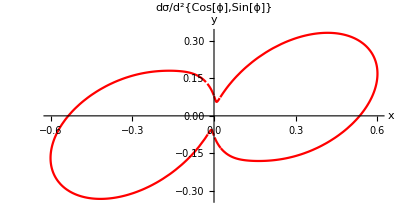

v_2=0.364805+1.18451×10^-18 ⅈ

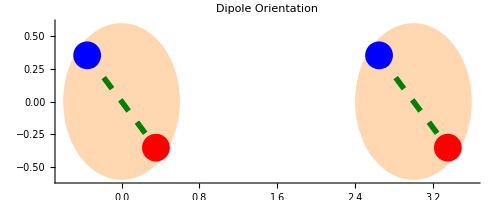

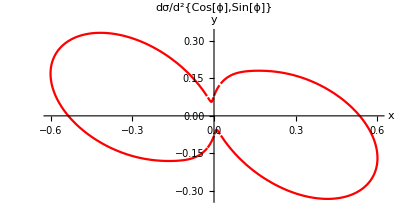

v_2=0.364805+3.09828×10^-18 ⅈ

```mathematica
x1u={1,1}/(2 Sqrt[2]);
x2u=-x1u;
x3u=x1u;
x4u=-x1u;
bu={3,0};
kT=1.0;
showdσ[bu,x1u,x2u,x3u,x4u,kT]
x1u={-1,1}/(2 Sqrt[2]);
x2u=-x1u;
x3u=x1u;
x4u=-x1u;
bu={3,0};
kT=1.0;
showdσ[bu,x1u,x2u,x3u,x4u,kT]
```

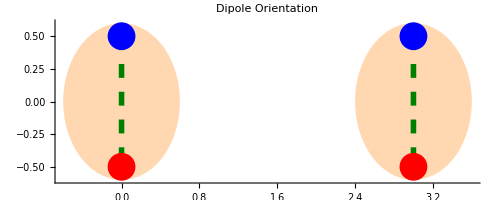

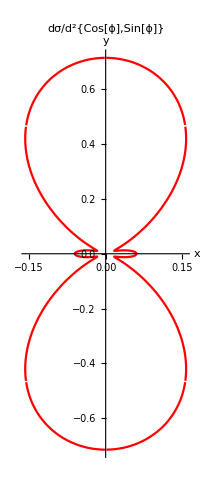

v_2=-0.669888-3.62969×10^-18 ⅈ

```mathematica
x1u={0,1/2};
x2u=-x1u;
x3u=x1u;
x4u=-x1u;
bu={3,0};
kT=1.0;
showdσ[bu,x1u,x2u,x3u,x4u,kT]
```

Therefore, we have v2 in hadron - hadron collisions.

### kT>>1/r

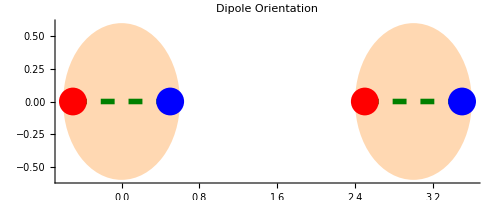

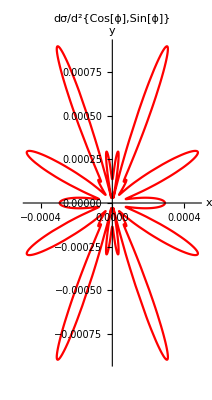

v_2=-0.0641272+0. ⅈ

```mathematica
x1u={1/2,0};
x2u={-1/2,0};
x3u={1/2,0};
x4u={-1/2,0};
bu={3,0};
kT=10.0;
showdσ[bu,x1u,x2u,x3u,x4u,kT]
```

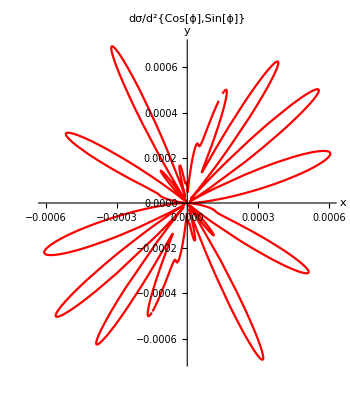

v_2=-0.0142743+0. ⅈ

-Graphics-

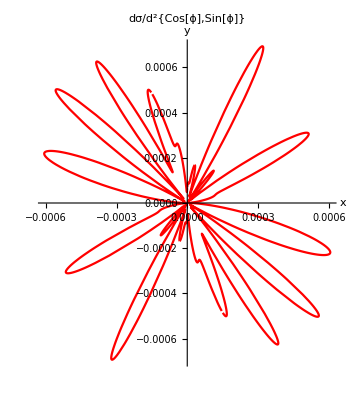

v_2=-0.0142743+0. ⅈ

```mathematica
kT=10.0;
x1u={1,1}/(2 Sqrt[2]);
x2u=-x1u;
x3u=x1u;
x4u=-x1u;
bu={3,0};
showdσ[bu,x1u,x2u,x3u,x4u,kT]
x1u={-1,1}/(2 Sqrt[2]);
x2u=-x1u;
x3u=x1u;
x4u=-x1u;
bu={3,0};
showdσ[bu,x1u,x2u,x3u,x4u,kT]
```

-Graphics-

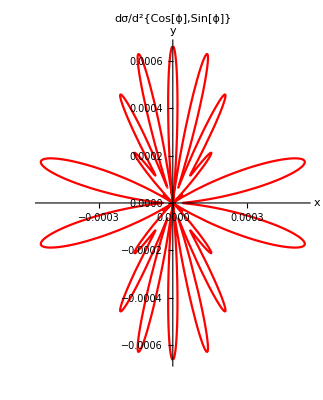

v_2=-0.0402007+0. ⅈ

```mathematica
x1u={0,1/2};
x2u=-x1u;
x3u=x1u;
x4u=-x1u;
bu={3,0};
kT=10.0;
showdσ[bu,x1u,x2u,x3u,x4u,kT]
```

Conclusion : for large k_T, the two partons can be treated as independent and the soft gluon can be taken as radiated uncoherently from the two individual partons.

### kT<<1/r

-Graphics-

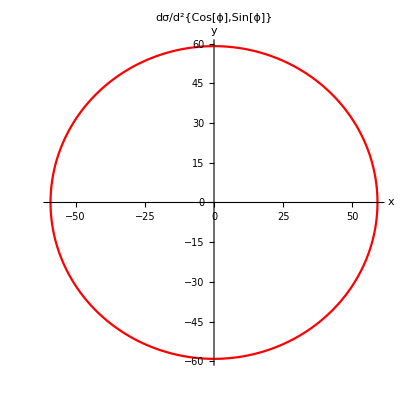

v_2=0.000347844+9.38067×10^-19 ⅈ

```mathematica
x1u={1/2,0};
x2u={-1/2,0};
x3u={1/2,0};
x4u={-1/2,0};
bu={3,0};
kT=0.1;
showdσ[bu,x1u,x2u,x3u,x4u,kT]
```

-Graphics-

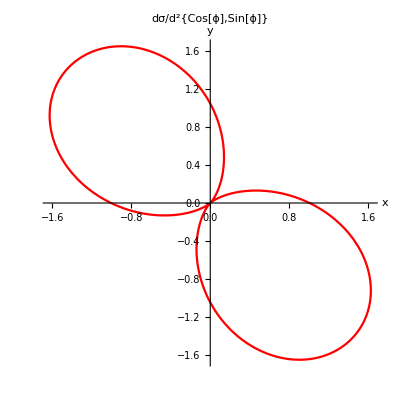

v_2=-0.0103349+8.84144×10^-19 ⅈ

-Graphics-

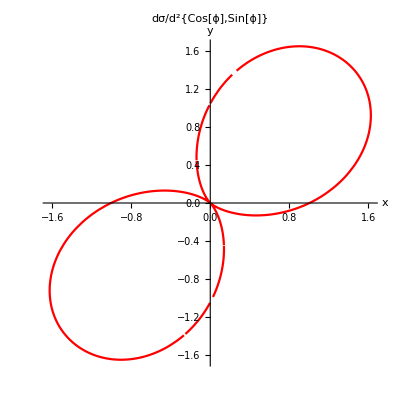

v_2=-0.0103349-2.30944×10^-19 ⅈ

```mathematica
x1u={1,1}/Sqrt[8];
x2u=-x1u;
x3u=x1u;
x4u=-x1u;
bu={3,0};
kT=0.1;
showdσ[bu,x1u,x2u,x3u,x4u,kT]
x1u={-1,1}/Sqrt[8];
x2u=-x1u;
x3u=x1u;
x4u=-x1u;
bu={3,0};
kT=0.1;
showdσ[bu,x1u,x2u,x3u,x4u,kT]
```

-Graphics-

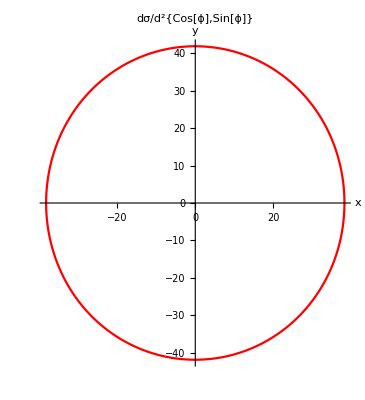

v_2=-0.0226608-1.3638×10^-18 ⅈ

```mathematica
x1u={0,1/2};
x2u=-x1u;
x3u=x1u;
x4u=-x1u;
bu={3,0};
kT=0.1;
showdσ[bu,x1u,x2u,x3u,x4u,kT]
```

Conclusion : for small k_T, radiation from the two partons can not distinguish the seperation of the dipole, hence v_2 is also negligible.